```mathematica
NilpotentQ[M_List]:=Module[{},
TrueQ[First[Eigenvalues[M]//DeleteDuplicates]==0]
]
```

```mathematica
Ma={{0,0},{1,0}}

Ma={{0,1,2},{0,0,3},{0,0,0}}
Ma={{5,-3,2},{15,-9,6},{10,-6,4}}

Ma//MatrixForm

vrs={x,y,z}
NilpotentQ[Ma]
Classifier`NilpotentSystemQ[Ma.vrs,vrs]
D[fnc[X],X]//FullForm
```

{{0,0},{1,0}}

{{0,1,2},{0,0,3},{0,0,0}}

{{5,-3,2},{15,-9,6},{10,-6,4}}

(5 | -3 | 2
15 | -9 | 6
10 | -6 | 4)

{x,y,z}

NilpotentQ[{{5,-3,2},{15,-9,6},{10,-6,4}}]

True

Derivative[1][fnc][X]

```mathematica
NilpotentQ[{{0,2},{0,0}}]
```

NilpotentQ[{{0,2},{0,0}}]

```mathematica
Derivative[1][fnc][T]
```

fnc'[T]

```mathematica
inv=NilpotentMethod`NilpotentReachSet[{x^2+y^2+z^2<1/10,{Ma.vrs,vrs,True},True}]
```

System is nilpotent.

{x[Pegasus`TIMEVARIABLE$6184],y[Pegasus`TIMEVARIABLE$6184],z[Pegasus`TIMEVARIABLE$6184]}

{x'[Pegasus`TIMEVARIABLE$6184],y'[Pegasus`TIMEVARIABLE$6184],z'[Pegasus`TIMEVARIABLE$6184]}=={5 x[Pegasus`TIMEVARIABLE$6184]-3 y[Pegasus`TIMEVARIABLE$6184]+2 z[Pegasus`TIMEVARIABLE$6184],15 x[Pegasus`TIMEVARIABLE$6184]-9 y[Pegasus`TIMEVARIABLE$6184]+6 z[Pegasus`TIMEVARIABLE$6184],10 x[Pegasus`TIMEVARIABLE$6184]-6 y[Pegasus`TIMEVARIABLE$6184]+4 z[Pegasus`TIMEVARIABLE$6184]}

{x→x[Pegasus`TIMEVARIABLE$6184],y→y[Pegasus`TIMEVARIABLE$6184],z→z[Pegasus`TIMEVARIABLE$6184]}

{C[1]→x,C[2]→y,C[3]→z}

x^2+y^2+z^2<1/10||(5 x-3 y+2 z≠0&&5 x^2+12 x y-9 y^2+12 x z+4 z^2≥0&&13 x^2-6 x y+5 y^2-4 x z-12 y z+10 z^2<7/5)

```mathematica
LZZ`InvS[inv,Ma.vrs,vrs, True]
```

True

```mathematica
Show[
RegionPlot3D[inv,{x,-1,1},{y,-1,1},{z,-1,1}]
]
```

-Graphics3D-

```mathematica
vrs={x,y}
vrsT=Map[#[t]&, vrs]
X[t_]=vrsT
```

{x,y}

{x[t],y[t]}

{x[t],y[t]}

```mathematica
syst=X'[t]==Ma.X[t]
```

{x'[t],y'[t]}=={-y[t]/4,y[t]}

```mathematica
sol=DSolve[syst,vrs,t]
```

{{x→Function[{t},C[1]+1/4 (1-ⅇ^t) C[2]],y→Function[{t},ⅇ^t C[2]]}}

```mathematica
init=1/2(x-1/2)^2+y^2≤1
```

1/2 (-1/2+x)^2+y^2≤1

```mathematica
initT=init/.{x->x[t], y->y[t]}
```

1/2 (-1/2+x[t])^2+y[t]^2≤1

```mathematica
initTT=(initT/.sol/.{C[1]->x,C[2]->y})[[1]]
```

ⅇ^(2 t) y^2+1/2 (-1/2+x+1/4 (1-ⅇ^t) y)^2≤1

```mathematica
initsol=Resolve[Exists[{t},initTT && t<0],Reals]
```

(x≤1/4 (2-√33)&&2-4 √2-4 x<y≤2+4 √2-4 x)||(x≤1/4 (2-√33)&&2+4 √2-4 x<y<2+√33-4 x)||(x≤1/4 (2-√33)&&y==2+√33-4 x)||(1/4 (2-√33)<x<1/2 (1-2 √2)&&2-4 √2-4 x<y≤2+4 √2-4 x)||(1/4 (2-√33)<x<1/2 (1-2 √2)&&2+4 √2-4 x<y<2+√33-4 x)||(1/4 (2-√33)<x<1/2 (1-2 √2)&&y==2+√33-4 x)||(x==1/2 (1-2 √2)&&y==0)||(x==1/2 (1-2 √2)&&0<y≤8 √2)||(x==1/2 (1-2 √2)&&8 √2<y<4 √2+√33)||(x==1/2 (1-2 √2)&&y==4 √2+√33)||(1/66 (33-16 √33)<x<1/2 (1+2 √2)&&y==2-√33-4 x)||(1/2 (1-2 √2)<x≤1/66 (33-16 √33)&&-(√(7+4 x-4 x^2))/(2 √2)<y<2-4 √2-4 x)||(1/66 (33-16 √33)<x≤1/66 (33-62 √2)&&2-√33-4 x<y<-(√(7+4 x-4 x^2))/(2 √2))||(1/66 (33-62 √2)<x<1/2 (1+2 √2)&&2-√33-4 x<y<2-4 √2-4 x)||(1/66 (33-16 √33)<x<(√2)/33+1/66 (33-64 √2)&&-(√(7+4 x-4 x^2))/(2 √2)≤y<2-4 √2-4 x)||((√2)/33+1/66 (33-64 √2)<x<1/2 (1+2 √2)&&2-4 √2-4 x≤y<-(√(7+4 x-4 x^2))/(2 √2))||(1/2 (1-2 √2)<x≤1/66 (33-16 √33)&&2-4 √2-4 x≤y<0)||(1/66 (33-16 √33)<x≤(√2)/33+1/66 (33-64 √2)&&2-4 √2-4 x≤y<0)||((√2)/33+1/66 (33-64 √2)<x<1/2 (1+2 √2)&&-(√(7+4 x-4 x^2))/(2 √2)≤y<0)||(1/2 (1-2 √2)<x<1/2 (1+2 √2)&&y==0)||(1/2 (1-2 √2)<x<-(√2)/33+1/66 (33+64 √2)&&(√(7+4 x-4 x^2))/(2 √2)<y≤2+4 √2-4 x)||(1/2 (1-2 √2)<x≤-(√2)/33+1/66 (33+64 √2)&&0<y≤(√(7+4 x-4 x^2))/(2 √2))||(-(√2)/33+1/66 (33+64 √2)<x<1/66 (33+16 √33)&&0<y≤2+4 √2-4 x)||(x==1/66 (33+16 √33)&&0<y≤2+4 √2-2/33 (33+16 √33))||(1/66 (33+16 √33)<x<1/2 (1+2 √2)&&0<y≤2+4 √2-4 x)||(1/2 (1-2 √2)<x≤1/66 (33+62 √2)&&2+4 √2-4 x<y<2+√33-4 x)||(1/66 (33+62 √2)<x<1/66 (33+16 √33)&&(√(7+4 x-4 x^2))/(2 √2)<y<2+√33-4 x)||(-(√2)/33+1/66 (33+64 √2)<x<1/66 (33+16 √33)&&2+4 √2-4 x<y≤(√(7+4 x-4 x^2))/(2 √2))||(x==1/66 (33+16 √33)&&2+4 √2-2/33 (33+16 √33)<y<1/(√33))||(1/66 (33+16 √33)<x<1/2 (1+2 √2)&&2+4 √2-4 x<y<(√(7+4 x-4 x^2))/(2 √2))||(1/2 (1-2 √2)<x<1/66 (33+16 √33)&&y==2+√33-4 x)||(x==1/2 (1+2 √2)&&y==-4 √2-√33)||(x==1/2 (1+2 √2)&&-4 √2-√33<y<-8 √2)||(x==1/2 (1+2 √2)&&-8 √2≤y<0)||(x==1/2 (1+2 √2)&&y==0)||(1/2 (1+2 √2)<x<1/4 (2+√33)&&y==2-√33-4 x)||(1/2 (1+2 √2)<x<1/4 (2+√33)&&2-√33-4 x<y<2-4 √2-4 x)||(1/2 (1+2 √2)<x<1/4 (2+√33)&&2-4 √2-4 x≤y<2+4 √2-4 x)||(x≥1/4 (2+√33)&&y==2-√33-4 x)||(x≥1/4 (2+√33)&&2-√33-4 x<y<2-4 √2-4 x)||(x≥1/4 (2+√33)&&2-4 √2-4 x≤y<2+4 √2-4 x)

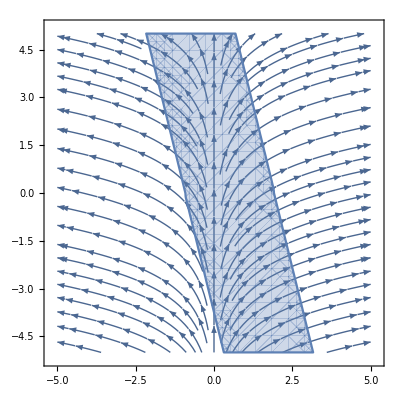

```mathematica
Show[
StreamPlot[{x,1},{x,-5,5},{y,-5,5}],
(*RegionPlot[init,{x,-5,5},{y,-5,5}],*)
RegionPlot[initsol,{x,-5,5},{y,-5,5}]
]
```